# Proof for 1D chain

## First P = phi_0(x1,x2), Q=phi_0(λ y1,λ x2). |x| = λ |y|, and optimum eq

```mathematica
ClearAll["Global`*"]
P=Subscript[c, 1]/(Subscript[x, 1]-Subscript[A, 1]) + Subscript[c, 2]/(Subscript[x, 2]-Subscript[A, 2]) (Subscript[x, 1]+Subscript[B, 1])/(Subscript[x, 1]-Subscript[A, 1]) 
Q=Subscript[c, 1]/(λ Subscript[y, 1]-Subscript[A, 1]) + Subscript[c, 2]/(λ Subscript[x, 2]-Subscript[A, 2]) (λ Subscript[y, 1]+Subscript[B, 1])/(λ Subscript[y, 1]-Subscript[A, 1]) 
S =Subscript[x, 1]+Subscript[x, 2] - λ (Subscript[y, 1]+Subscript[x, 2])
(*diff=(Subscript[y, 1]+Subscript[B, 1])(Subscript[y, 1]-Subscript[A, 1])/(Subscript[A, 1]+Subscript[B, 1]) -(Subscript[x, 2]+Subscript[B, 2])(Subscript[x, 2]-Subscript[A, 2])/(Subscript[A, 2]+Subscript[B, 2]) *)
diff=D[P,Subscript[x, 1]]-D[P,Subscript[x, 2]];
diff=diff/.{Subscript[x, 1]->Subscript[y, 1]}
```

c_1/(-A_1+x_1)+(c_2 (B_1+x_1))/((-A_1+x_1) (-A_2+x_2))

c_1/(-A_1+λ y_1)+(c_2 (B_1+λ y_1))/((-A_2+λ x_2) (-A_1+λ y_1))

x_1+x_2-λ (x_2+y_1)

-c_1/(-A_1+y_1)^2+c_2/((-A_2+x_2) (-A_1+y_1))-(c_2 (B_1+y_1))/((-A_2+x_2) (-A_1+y_1)^2)+(c_2 (B_1+y_1))/((-A_2+x_2)^2 (-A_1+y_1))

## Rewrite P-Q=0, solve y1 from |x|=λ|y|

```mathematica
PQ=Numerator[Factor[P-Q]];
Collect[Factor[PQ],λ]
y1sol=Solve[S==0,Subscript[y, 1]]
```

-A_2^2 c_1 x_1+A_1 A_2 c_2 x_1+A_2 B_1 c_2 x_1+A_1 B_1 c_2 x_2+A_2 c_1 x_1 x_2-B_1 c_2 x_1 x_2+λ (-A_1 B_1 c_2 x_2+A_2 c_1 x_1 x_2-A_1 c_2 x_1 x_2-c_1 x_1 x_2^2+A_2^2 c_1 y_1-A_1 A_2 c_2 y_1-A_2 B_1 c_2 y_1-A_2 c_1 x_2 y_1+A_1 c_2 x_2 y_1-c_2 x_1 x_2 y_1)+λ^2 (-A_2 c_1 x_2 y_1+B_1 c_2 x_2 y_1+c_2 x_1 x_2 y_1+c_1 x_2^2 y_1)

{{y_1→(x_1+x_2-λ x_2)/λ}}

## Substitute y1 solution into P-Q, factorise. Introduce positive parameters for x_1,x_2. Either λ=1 or not. In λ=1 we have the following optimum eq.

```mathematica
PQfac=Factor[PQ/.y1sol][[1]]
xxi={Subscript[x, 1]->Subscript[A, 1]+Subscript[ξ, 1],Subscript[x, 2]->Subscript[A, 2]+Subscript[ξ, 2]}
opteq=Factor[diff/.y1sol/.xxi/.{λ->1}]//Numerator
opteq=Collect[Factor[diff/.y1sol/.xxi]//Numerator,λ,Factor]
```

-(-1+λ) x_2 (A_2^2 c_1-A_1 A_2 c_2+A_1 B_1 c_2-A_2 B_1 c_2+A_1 c_2 x_1-B_1 c_2 x_1-c_2 x_1^2-A_2 c_1 x_2-λ A_2 c_1 x_2+A_1 c_2 x_2+λ B_1 c_2 x_2-c_2 x_1 x_2+λ c_2 x_1 x_2+λ c_1 x_2^2)

{x_1→A_1+ξ_1,x_2→A_2+ξ_2}

{A_1 c_2 ξ_1+B_1 c_2 ξ_1+c_2 ξ_1^2-A_1 c_2 ξ_2-B_1 c_2 ξ_2-c_1 ξ_2^2}

{c_2 (A_1+A_2+ξ_1+ξ_2)^2-λ c_2 (A_1+A_2+ξ_1+ξ_2) (A_1+2 A_2-B_1+2 ξ_2)+λ^2 (A_1 A_2 c_2+A_2^2 c_2-A_1 B_1 c_2-A_2 B_1 c_2+2 A_2 c_2 ξ_2-2 B_1 c_2 ξ_2-c_1 ξ_2^2+c_2 ξ_2^2)}

## Now find the other factor in P-Q, solve for λ, and note that this λ is greater than 1 unless the ξ’s satisfy the optimum eq.

```mathematica
factorlist=FactorList[PQfac];
remaining=factorlist[[4]][[1]]/.xxi
lambdaremaining=Solve[(remaining/.xxi)==0,λ]
lambdaremaining = λ/.lambdaremaining
Factor[Numerator[lambdaremaining]-Denominator[lambdaremaining]]
opteq
```

A_2^2 c_1-A_1 A_2 c_2+A_1 B_1 c_2-A_2 B_1 c_2+A_1 c_2 (A_1+ξ_1)-B_1 c_2 (A_1+ξ_1)-c_2 (A_1+ξ_1)^2-A_2 c_1 (A_2+ξ_2)-λ A_2 c_1 (A_2+ξ_2)+A_1 c_2 (A_2+ξ_2)+λ B_1 c_2 (A_2+ξ_2)-c_2 (A_1+ξ_1) (A_2+ξ_2)+λ c_2 (A_1+ξ_1) (A_2+ξ_2)+λ c_1 (A_2+ξ_2)^2

{{λ→(A_1 A_2 c_2+A_2 B_1 c_2+A_1 c_2 ξ_1+A_2 c_2 ξ_1+B_1 c_2 ξ_1+c_2 ξ_1^2+A_2 c_1 ξ_2+c_2 ξ_1 ξ_2)/((A_2+ξ_2) (A_1 c_2+B_1 c_2+c_2 ξ_1+c_1 ξ_2))}}

{(A_1 A_2 c_2+A_2 B_1 c_2+A_1 c_2 ξ_1+A_2 c_2 ξ_1+B_1 c_2 ξ_1+c_2 ξ_1^2+A_2 c_1 ξ_2+c_2 ξ_1 ξ_2)/((A_2+ξ_2) (A_1 c_2+B_1 c_2+c_2 ξ_1+c_1 ξ_2))}

{A_1 c_2 ξ_1+B_1 c_2 ξ_1+c_2 ξ_1^2-A_1 c_2 ξ_2-B_1 c_2 ξ_2-c_1 ξ_2^2}

{c_2 (A_1+A_2+ξ_1+ξ_2)^2-λ c_2 (A_1+A_2+ξ_1+ξ_2) (A_1+2 A_2-B_1+2 ξ_2)+λ^2 (A_1 A_2 c_2+A_2^2 c_2-A_1 B_1 c_2-A_2 B_1 c_2+2 A_2 c_2 ξ_2-2 B_1 c_2 ξ_2-c_1 ξ_2^2+c_2 ξ_2^2)}

```mathematica
(remaining/opteq)/.{λ->1}//Factor
```

{-1}

```mathematica
Factor[(remaining - opteq)/.{λ->0}]
```

{-A_1^2 c_2-3 A_1 A_2 c_2-A_2^2 c_2-A_2 B_1 c_2-3 A_1 c_2 ξ_1-3 A_2 c_2 ξ_1-B_1 c_2 ξ_1-2 c_2 ξ_1^2-A_2 c_1 ξ_2-2 A_1 c_2 ξ_2-2 A_2 c_2 ξ_2-3 c_2 ξ_1 ξ_2-c_2 ξ_2^2}

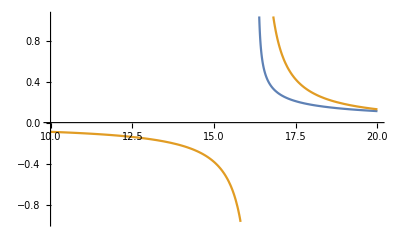

```mathematica
Plot[{3/(4 Sqrt[3 x (-7+Sqrt[3 x])]),3/(12 x - 28 Sqrt[ 3 x])},{x,10,20}]
```